```mathematica
F1=a N^m /(1+a h N^m)
F2=c N^β / (b+N^β)
```

(a N^m)/(1+a h N^m)

(c N^β)/(b+N^β)

```mathematica
parms1={a->2,h->2,m->3}
parms2={c->1/h,b->1/(a h),β->m}/.parms1
```

{a→2,h→2,m→3}

{c→1/2,b→1/4,β→3}

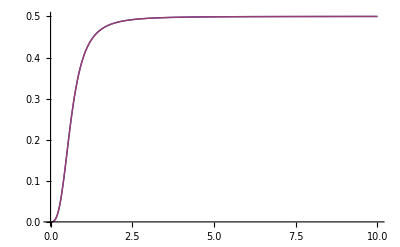

```mathematica
Plot[{F1/.parms1,F2/.parms2},{N,0,10},PlotRange->Full]
```